{{43,57,0,0,0,0,0,0,0,0,0,0},{13,30,21,36,0,0,0,0,0,0,0,0},{6,12,24,13,26,18,0,0,0,0,0,0},{3,10,9,21,12,10,24,11,0,0,0,0},{2,7,7,9,18,11,4,17,16,9,0,0},{2,5,7,6,9,15,10,3,8,18,11,7}}

{100,100,99,100,100,101}

0.0228227 (2-Cos[t]-Sin[t]+t Sin[t]^2+Sin[t]^10)

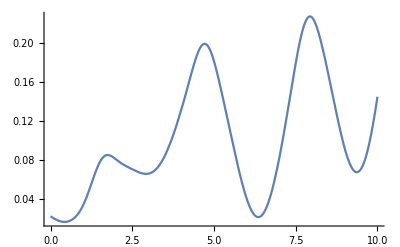

```mathematica
T=RandomInteger[{1,10}];
stake =100;
f[x_] = (x*Sin[x]^2+D[Cos[x],{x,T}]+D[Sin[x],{x,T}]+Sin[x]^T+2);
F[x_] = f[t]/NIntegrate[f[t],{t,0,T}];
S = Table[Table[Round[stake*NIntegrate[F[t],{t,i*T/rounds,(i+1)*T/rounds}]],{i,0,rounds-1}],{rounds,2,12,2}];
padS = Table[PadRight[Part[S,i],12],{i,1,6}]
check=Table[Sum[Part[padS,i,j],{j,1,Length[Part[S,i]]}],{i,1,6}]
F[x]
Plot[F[t],{t,0,T},PlotRange->Full ]
```